```mathematica
SetDirectory["C:\\Users\\physk\\OneDrive\\Desktop\\Oomega Resonance with eta_0 no Betamax"];
```

```mathematica
(* Extract Data Files and save them as a List *)
filestart=0.1;
Δfilenum=0.1;
numfiles=20;
fileend=filestart + Δfilenum*(numfiles-1);
VaryOmegaDataD=Table[ReadList["Non-Markovian Entanglement Omega_"<>ToString[NumberForm[omegavalue, {3, 2}]]<>".txt"], {omegavalue, filestart, fileend,Δfilenum}];
```

```mathematica
ListAnimate[Table[ListLinePlot[{VaryOmegaDataD[[file]][[1]], VaryOmegaDataD[[file]][[2]]}, PlotRange->All], {file, 1, 20}], AnimationRunning->False]
```

```mathematica
(* Ω/ω = 0.1 ,..., 2.00 *)
(* We find that the average value from 400 to 2000 reaches a maximum stable value for frequency ratio of Ω/ω = 1.00 *)
oscillator12=ParallelTable[{file/10, Mean[Table[VaryOmegaDataD[[file]][[1]][[value]][[2]], {value, 400, 2000}]]}, {file, 1, 20}];
oscillator34=ParallelTable[{file/10, Mean[Table[VaryOmegaDataD[[file]][[2]][[value]][[2]], {value, 400, 2000}]]}, {file, 1, 20}];
```

```mathematica
osc12max=oscillator12[[10]][[2]]
osc34max=oscillator34[[10]][[2]]
```

0.120598

1.56325

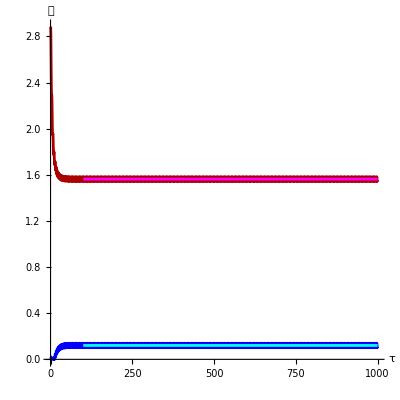
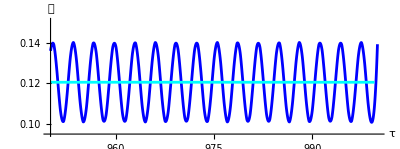
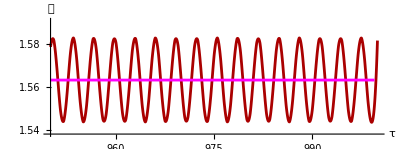

```mathematica
height=400;
width=400;
PlotFormat1={ImageSize->{UpTo[width], UpTo[height]}, AspectRatio->height/width,  AxesLabel->{"τ", "𝒩"}, AxesStyle->Directive[Black, 23], BaseStyle->{FontFamily->"Latin Modern Roman"},  LabelStyle->Directive[Black, 23], PlotRange->All};

Osc1234plot=Show[{ListLinePlot[{VaryOmegaDataD[[10]][[1]][[1;;2000]], VaryOmegaDataD[[10]][[2]][[1;;2000]]}, PlotStyle->{Directive[Blue], Directive[Darker[Red], Thickness->0.005]}, Evaluate[PlotFormat1]], Plot[{osc12max, osc34max}, {x, 100, 1000}, PlotStyle->{Directive[Cyan, Thickness->0.005], Directive[Magenta, Thickness->0.005]}]}];

Ifunc12zoom=Interpolation[VaryOmegaDataD[[10]][[1]][[400;;2000]]];
Ifunc34zoom=Interpolation[VaryOmegaDataD[[10]][[2]][[400;;2000]]];

height=140;
width=375;
ZoomFormat={ImageSize->{UpTo[width], UpTo[height]}, AspectRatio->height/width,  AxesLabel->{"τ", "𝒩"}, AxesStyle->Directive[Black, 14], BaseStyle->{FontFamily->"Latin Modern Roman"},  LabelStyle->Directive[Black, 14], PlotRange->All};

zoom12plot=Show[Plot[Ifunc12zoom[x], {x, 950, 999.95}, PlotStyle->Directive[Blue, Thickness->0.005], PlotRange->{0.095, 0.151}, Evaluate[ZoomFormat]], Plot[osc12max, {x, 950, 999.5}, PlotStyle->{Directive[Cyan, Thickness->0.005]}]];
zoom34plot=Show[Plot[Ifunc34zoom[x], {x, 950, 999.95}, PlotStyle->Directive[Darker[Red], Thickness->0.005], PlotRange->{1.538
, 1.591}, Evaluate[ZoomFormat]], Plot[osc34max, {x, 950, 999.5}, PlotStyle->{Directive[Magenta, Thickness->0.005]}]];

Osc1234plotwithzoom=Overlay[{Overlay[{Osc1234plot, zoom12plot}, Alignment->{0.75, -0.55}], zoom34plot}, Alignment->{0.75, 0.65}]
```

```mathematica
height=400;
width=400;
PlotFormat2={ImageSize->{UpTo[width], UpTo[height]}, AspectRatio->height/width,  AxesLabel->{"Ω/ω", "𝒩"}, AxesStyle->Directive[Black, 23], BaseStyle->{FontFamily->"Latin Modern Roman"},  LabelStyle->Directive[Black, 23]};

osc12plot=Show[ListLinePlot[oscillator12, PlotStyle->Directive[Blue, Dashed], PlotRange->{0, 0.126}, Evaluate[PlotFormat2], Ticks->{Automatic, Automatic}], ListPlot[oscillator12, PlotStyle->Directive[Black, PointSize->0.015]], Plot[osc12max, {x, 0, 2}, PlotRange->{0, 1.60}, PlotStyle->Directive[Cyan], Evaluate[PlotFormat2]], ListPlot[{oscillator12[[10]]}, PlotStyle->Directive[Cyan, PointSize->0.016]]];

osc34plot=Show[ListLinePlot[oscillator34, PlotStyle->Directive[Red, Dashed], PlotRange->{0, 1.60}, Evaluate[PlotFormat2], Ticks->{Automatic, {0.36, 0.76, 1.16, 1.56}}], ListPlot[oscillator34, PlotStyle->Directive[Black, PointSize->0.015]], Plot[osc34max, {x, 0, 2}, PlotRange->{0, 1.60}, PlotStyle->Directive[Magenta], Evaluate[PlotFormat2]], ListPlot[{oscillator34[[10]]}, PlotStyle->Directive[Magenta, PointSize->0.016]]];

ResonanceNobetamaxNoeta=Rasterize[Row[{Osc1234plotwithzoom, osc12plot, osc34plot}, ImageSize->{1200, 400}]]
```

-Graphics-

```mathematica
Export["ResonanceNobetamaxNoeta.png", ResonanceNobetamaxNoeta]
```

ResonanceNobetamaxNoeta.png